```mathematica
(*CRYSTAL FACTOR*)
```

```mathematica
mn=12;(*in GeV*)
n=10^36;(*in m^-3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
T=10^7;(*in K*)
```

```mathematica
z=6;
e=0.303;
vesc=6*10^6;(*in m/s*)
esup[mx_]:=(z^2*e^2*mx*n*1.98^3*10^-48)/(kb*T*6.242*10^9*mn^2);(*in GeV*)
en[mx_]:=0.5*mx*(vesc/(3*10^8))^2;(*in GeV, maximum energy*)
```

```mathematica
factor[mx_]:=1-Exp[(-en[mx])/esup[mx]];
```

```mathematica
invspacing=((4*π)/3*n)^(1/3)*2*10^-16//N(*in GeV*);
```

```mathematica
q[mx_]:=(mx*mn)/(mx+mn)*vesc/(3*10^8);(*in GeV*)
```

```mathematica
q[0.01]/invspacing
```

0.619834

```mathematica
LogLogPlot[1-factor[mx],{mx,0.01,10^6}, Frame->True]
```

-Graphics-

```mathematica
En[mx_]:=(q[mx])^2 mx/(2 mn^2)
```

```mathematica
factor2[mx_]:=1-Exp[(-En[mx])/esup[mx]];
```

```mathematica
q[1]//N
```

0.0184615

```mathematica
en[10^-18]
```

2.×10^-22

```mathematica
esup[10^-18]
```

2.06832×10^-25

```mathematica
factor2[1000]//N
```

1.

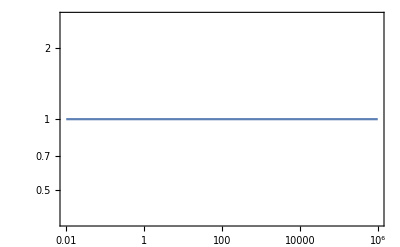

```mathematica
LogLogPlot[factor[mx],{mx,0.01,10^6}, Frame->True]
```

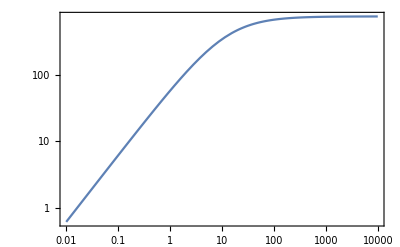

```mathematica
LogLogPlot[q[mx]/invspacing,{mx,0.01,10^4},Frame->True]
```